## Brian — PS 8 — 2025-02-18 — Solution

## EIWL3 Sections 20, 21, and 22

## Exercises from EIWL3 Section 20

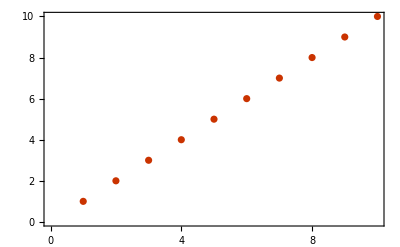

```mathematica
(* 20.1 *) ListPlot[Range[10], PlotTheme->"Web"]
```

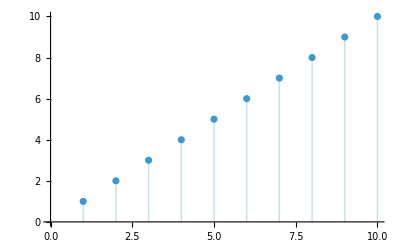

```mathematica
(* 20.2 *) ListPlot[Range[10],Filling->Axis]
(* That is interesting filling. I wonder if *)
(* Wolfram wanted a list line plot. *)
```

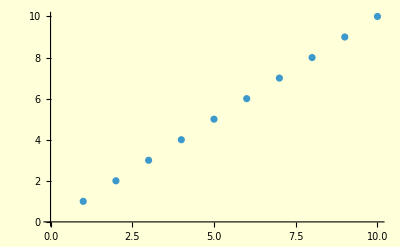

```mathematica
(* 20.3 *) ListPlot[Range[10],Background->LightYellow]
(* I couldn't bear the bright yellow so I dimmed it. *)
```

```mathematica
(* 20.4 *) GeoListPlot[Entity["Country","Australia"],GeoRange->All]
```

-Graphics-

```mathematica
(* 20.5 *) GeoListPlot[Entity["Country","Madagascar"],GeoRange->Entity["Ocean","IndianOcean"]]
```

-Graphics-

```mathematica
(* 20.6 *) GeoGraphics[EntityClass["Country","SouthAmerica"],GeoBackground->"ReliefMap"]
```

-Graphics-

```mathematica
(* 20.7 *) GeoListPlot[{,Entity["Country","Finland"],},GeoRange->Entity["GeographicRegion","Europe"],GeoLabels->True]
```

-Graphics-

```mathematica
(* 20.8 *) GeoListPlot[EntityClass["University","TheIvyLeague"],GeoLabels->True]
```

-Graphics-

```mathematica
(* 20.9 *)Style[Grid[ Table[x y,{x,12},{y,12} ],Background->Black],White]
(* Is this the way we were meant to solve this? Well it works. *)
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
(* 20.10 *) Table[Graphics[Disk[],ImageSize->RandomInteger[{1,40}]],100]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

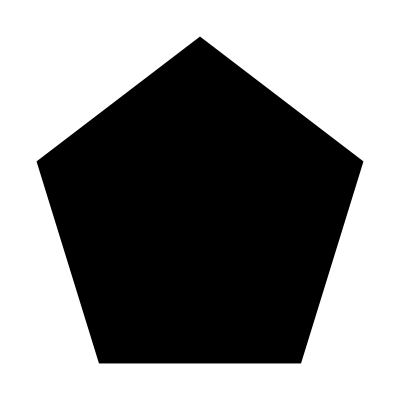
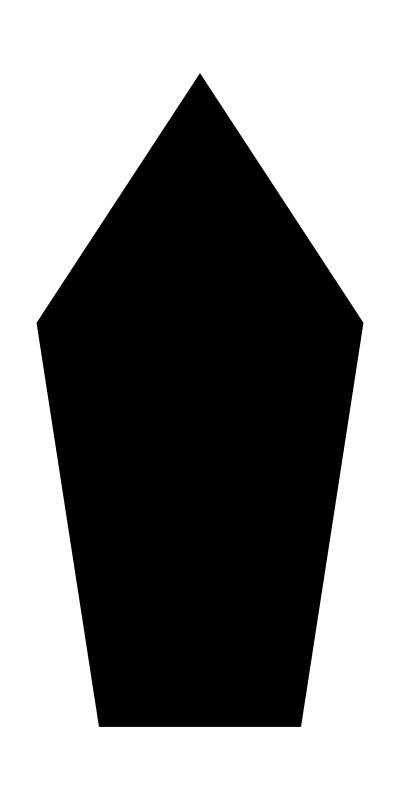
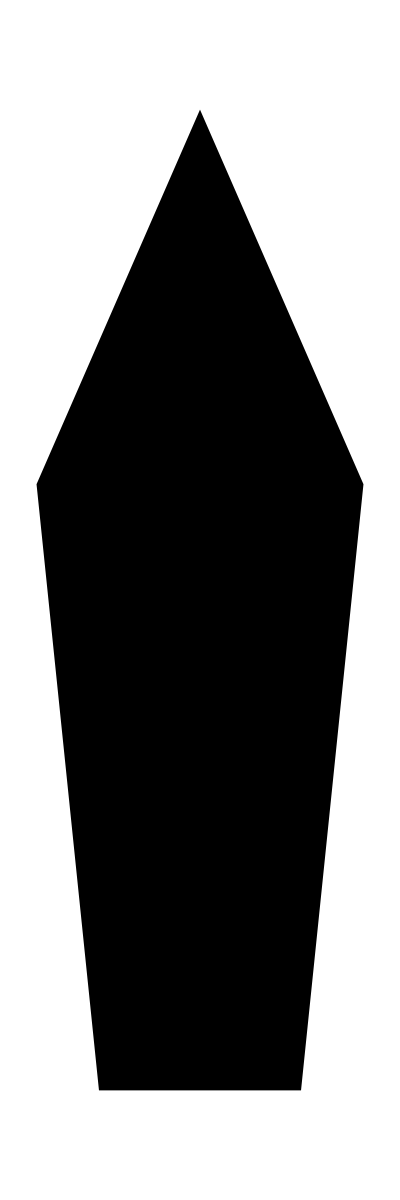
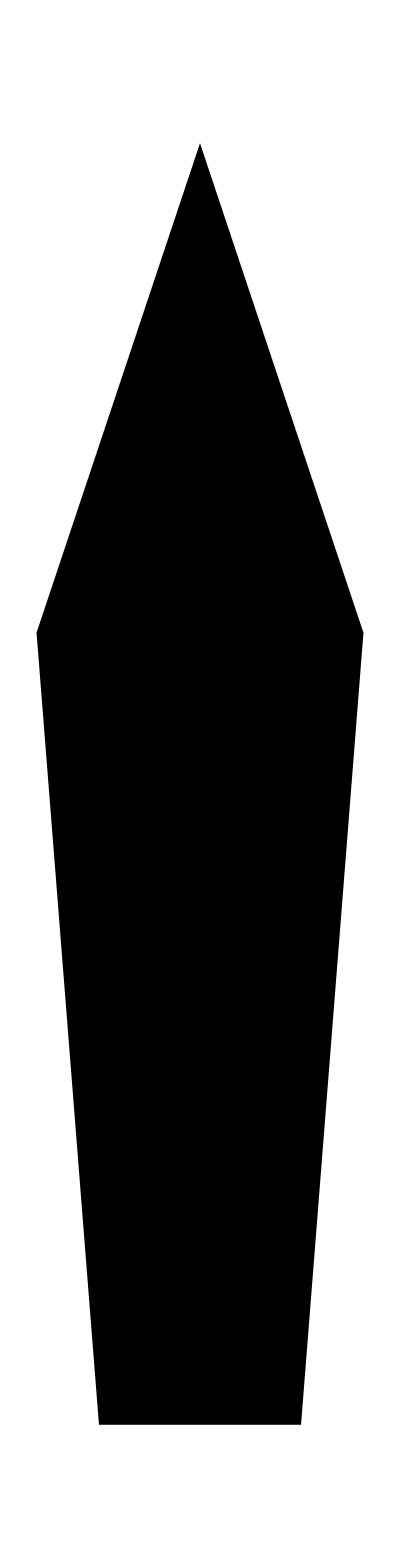
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 20.11 *) Table[Graphics[RegularPolygon[5],AspectRatio->aspectRatio],{aspectRatio,1,10}]
```

```mathematica
(* 20.12 *) Manipulate[Graphics[Circle[],ImageSize->size],{size,5,500}]
```

```mathematica
(* 20.13 *) Grid[Table[RandomColor[],{i,10},{j,10}],Frame->All]
```

RGBColor[0.8021552752038537, 0.06633731039288882, 0.44252649281599266] | RGBColor[0.6598902938464661, 0.4472489221574636, 0.23232904153279255] | RGBColor[0.21424444424064326, 0.3236128728610963, 0.014206876563805926] | RGBColor[0.26383307288343505, 0.6990412835920008, 0.2027165504209789] | RGBColor[0.5020531476930272, 0.6935213554079256, 0.9129130166370487] | RGBColor[0.7735818569622335, 0.8427047442958211, 0.3346412736790376] | RGBColor[0.6023352706534773, 0.8706689168969801, 0.5014047672872186] | RGBColor[0.5779809888838088, 0.763599465634947, 0.18574714669926684] | RGBColor[0.8052491348293056, 0.27771252638375366, 0.8529700823701967] | RGBColor[0.8314493959269929, 0.5743851603022925, 0.04272337154525818]
RGBColor[0.6905777570818972, 0.5951045021299457, 0.1813401519536606] | RGBColor[0.6077943430266735, 0.6704602581582382, 0.17047861087909655] | RGBColor[0.4474107675401635, 0.7678691747451503, 0.09262560296903488] | RGBColor[0.07501389179979068, 0.9255224744243633, 0.300868796903631] | RGBColor[0.25130511164022784, 0.369860744444533, 0.4054211413295463] | RGBColor[0.7292463072861515, 0.9895752855000011, 0.720559417103519] | RGBColor[0.9713881982976671, 0.6698508310938769, 0.6849282023083652] | RGBColor[0.6700749707878104, 0.6930407673225656, 0.351865269413973] | RGBColor[0.030898478157958653, 0.5053951943296213, 0.7055710429772528] | RGBColor[0.5402875053459462, 0.732520237717873, 0.44741502531852584]
RGBColor[0.9989611167684109, 0.17579817025968958, 0.9591952547008491] | RGBColor[0.17356938816410583, 0.5860566923367172, 0.3680356178208568] | RGBColor[0.8341123726356434, 0.4369844530790272, 0.37584536535019697] | RGBColor[0.3584191444797289, 0.2102768106929247, 0.2227608240732617] | RGBColor[0.9923665243238704, 0.2862987389710778, 0.17894765569394933] | RGBColor[0.9029213615557545, 0.48040837238554546, 0.4044181132690665] | RGBColor[0.7166592734494668, 0.9672292178056248, 0.7494677162298105] | RGBColor[0.6068555315445299, 0.5372042501058016, 0.30156134761603703] | RGBColor[0.3576504845124593, 0.8507711604646115, 0.8076171732916342] | RGBColor[0.18849543178595418, 0.7936155227104096, 0.5256781930350942]
RGBColor[0.4229273919627903, 0.2269957185952427, 0.6222488295078836] | RGBColor[0.8851015238682842, 0.543122725782452, 0.983083983467395] | RGBColor[0.37113609717609286, 0.615645207236009, 0.4289354967117873] | RGBColor[0.46066944205708826, 0.8411550577771987, 0.8752754831356524] | RGBColor[0.23968588886786524, 0.07242922000180796, 0.30306936437814413] | RGBColor[0.33145111545829464, 0.6559240675319953, 0.6191184660560125] | RGBColor[0.38228588263070495, 0.3834126597337195, 0.757470727169032] | RGBColor[0.9056425485003605, 0.17349421725217806, 0.10080996630189953] | RGBColor[0.47556289667810003, 0.9042908714923745, 0.3694021809256227] | RGBColor[0.019925173457621348, 0.1263908356684127, 0.6753092338479321]
RGBColor[0.5064298683218134, 0.4082852395645826, 0.2095777763852007] | RGBColor[0.7375098596461782, 0.325052215960802, 0.7487407981915346] | RGBColor[0.3950865143982534, 0.6329789107156123, 0.389929624559892] | RGBColor[0.7114545916816541, 0.48314102830806216, 0.6240011680953275] | RGBColor[0.46865504618399156, 0.55913179409944, 0.8319011621094028] | RGBColor[0.5111246469941051, 0.04938713176652154, 0.44362727216887876] | RGBColor[0.7119685068024246, 0.04807619947366559, 0.8180509779172298] | RGBColor[0.661423226645194, 0.27321888176159703, 0.9679885736816713] | RGBColor[0.2682589645068616, 0.06264714083692557, 0.9135136691933765] | RGBColor[0.23241961894364116, 0.32549961657222126, 0.6783249192702021]
RGBColor[0.5890312432672502, 0.2228694819842969, 0.6717778624890418] | RGBColor[0.41280362228552026, 0.5787403553472443, 0.36005995381299183] | RGBColor[0.05788409106783421, 0.46521006604373794, 0.6451156378870664] | RGBColor[0.8044167627688821, 0.5040428020529308, 0.8714350548804324] | RGBColor[0.2724630361764071, 0.7429142938049254, 0.3286028797264464] | RGBColor[0.3979687519147621, 0.2558105522230034, 0.35771702968890073] | RGBColor[0.7717794459673999, 0.2373604933310829, 0.310459262744766] | RGBColor[0.7610270475996197, 0.7466442565426417, 0.3610356544542692] | RGBColor[0.5075595844941685, 0.497344627707184, 0.5185512780019848] | RGBColor[0.5031974323262982, 0.1689582356704502, 0.5984368880524438]
RGBColor[0.2798031012470241, 0.8255725584984057, 0.7640613450980949] | RGBColor[0.3232860859390416, 0.575405307583231, 0.8947607676370104] | RGBColor[0.9589776873320965, 0.9958265066513023, 0.4028902083010626] | RGBColor[0.12222433086459894, 0.6792298307865763, 0.653391252559907] | RGBColor[0.5751942289240504, 0.5420787230872737, 0.3573971584976279] | RGBColor[0.9458521988394335, 0.2067443434085281, 0.3212439611371958] | RGBColor[0.5120904116989342, 0.5913792352542662, 0.8857607546031669] | RGBColor[0.16720360273391366, 0.1415440116552853, 0.9964676003371349] | RGBColor[0.31013670342100386, 0.6573294168084807, 0.31606074445405263] | RGBColor[0.6503156898535303, 0.4279800440290158, 0.8836553360666668]
RGBColor[0.9891672417795299, 0.29210520715570065, 0.09763378064603545] | RGBColor[0.8348825064256253, 0.7302708202127937, 0.22190622161579676] | RGBColor[0.7630930423091304, 0.9963647983919635, 0.8368266019734651] | RGBColor[0.7741820239634523, 0.8351658121604351, 0.6682743941230018] | RGBColor[0.024943094531969745, 0.44999845043565245, 0.009768156517061088] | RGBColor[0.5499651111305643, 0.0014413937129806875, 0.5692327399336203] | RGBColor[0.4004201085905761, 0.16323657762567811, 0.9150898932006744] | RGBColor[0.7479441819601604, 0.44337688524231167, 0.06891138693821963] | RGBColor[0.0121314955834666, 0.9448883981394887, 0.7673164473654543] | RGBColor[0.5742481570636302, 0.06904163526054696, 0.6641987740286515]
RGBColor[0.38106822048803424, 0.07140599923350988, 0.026336350461142466] | RGBColor[0.15205816898710878, 0.491208207346685, 0.2763672525858196] | RGBColor[0.2737041865704859, 0.8014325105740661, 0.9400811144573564] | RGBColor[0.45252823388920027, 0.8520366389991192, 0.5346233011239585] | RGBColor[0.725163070072061, 0.41899995925704725, 0.5584876728379813] | RGBColor[0.5125095554187298, 0.46753826232377693, 0.8912774011850468] | RGBColor[0.9934812380660751, 0.21084387149775385, 0.7498219090450016] | RGBColor[0.43600250563015175, 0.2840561114431974, 0.7126327988145305] | RGBColor[0.34214739776310865, 0.046006471335395815, 0.35043664635603067] | RGBColor[0.802338533525847, 0.2605045050537167, 0.025978814666503203]
RGBColor[0.45287397735121293, 0.8903491640712502, 0.9304966459967652] | RGBColor[0.7531204479289189, 0.8358793280880601, 0.6185133795203654] | RGBColor[0.27058783714647894, 0.03508602261453442, 0.4238497476006171] | RGBColor[0.6848594735273335, 0.6363615985435633, 0.19764238730611106] | RGBColor[0.4866333052939349, 0.7755821545152493, 0.5631804100224398] | RGBColor[0.34097381297485985, 0.06589700254858033, 0.8571123855395173] | RGBColor[0.1979006435839099, 0.8175683593052385, 0.6350848133344316] | RGBColor[0.15489152169098364, 0.03008203539193377, 0.6662152788548779] | RGBColor[0.0065584692114879495, 0.8825821045501854, 0.4825391512545285] | RGBColor[0.03481547940737961, 0.31007430945254866, 0.683952397456346]

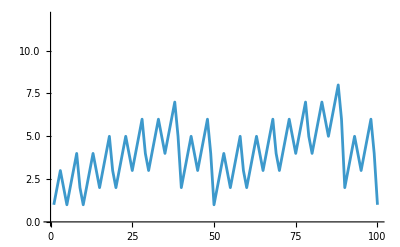

```mathematica
(* 20.24 *) ListLinePlot[
Table[StringLength[RomanNumeral[i]],{i,100}],
PlotRange->Max[Table[StringLength[RomanNumeral[i]],{i,1000}]]]
```

## Exercises from EIWL3 Section 21

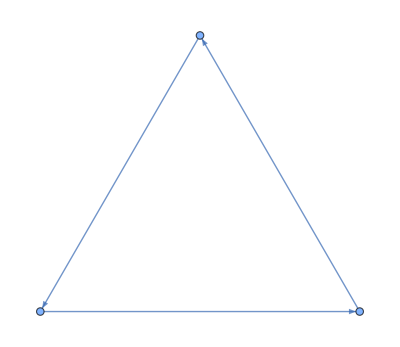

```mathematica
(* 21.1 *) Graph[{1->2,2->3,3->1}]
```

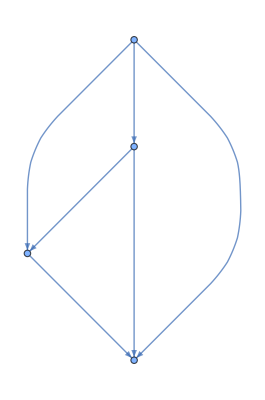

```mathematica
(* 21.2 *) Graph[{1->2,1->3,1->4,2->3,2->4,3->4}]
```

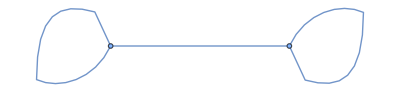
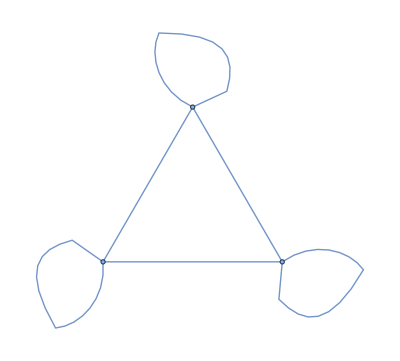
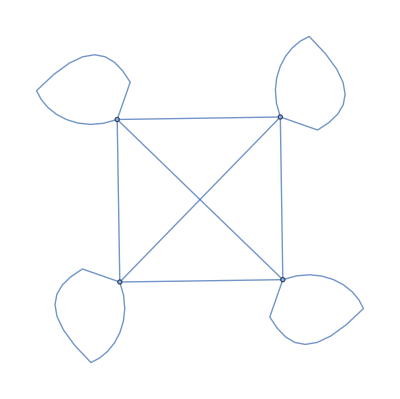
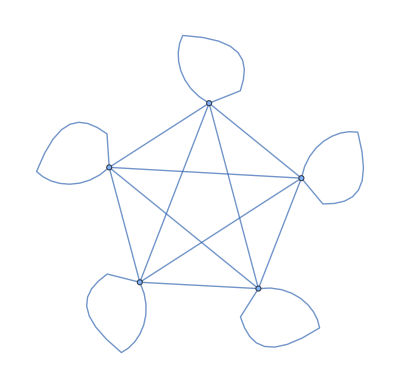
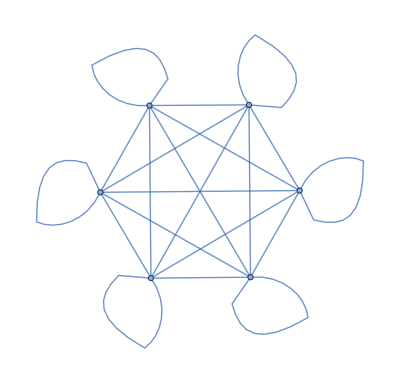
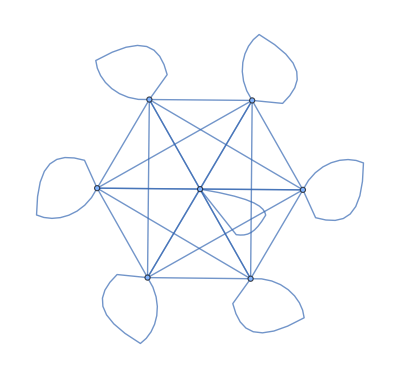
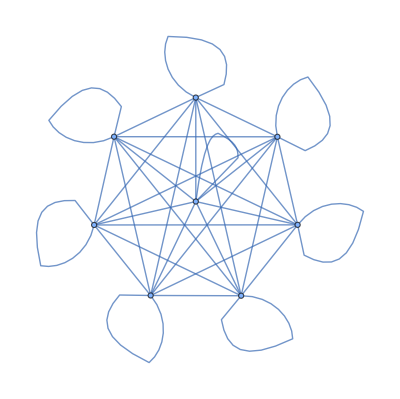
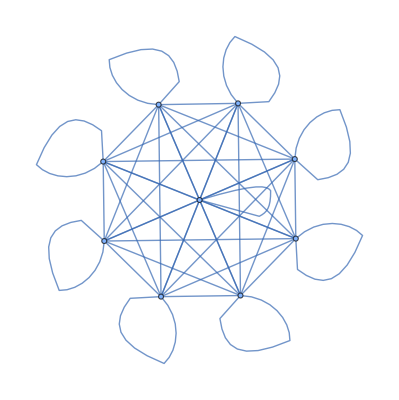

```mathematica
(* 21.3 *) Table[UndirectedGraph[Flatten[Table[i->j,{i,nodes},{j,nodes}]]],{nodes,2,10}]
```

```mathematica
(* 21.4 *) Flatten[Table[i,3,{i,2}]]
```

{1,2,1,2,1,2}

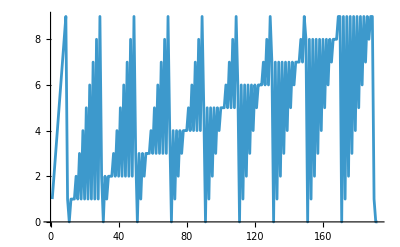

```mathematica
(* 21.5 *) ListLinePlot[Flatten[Table[IntegerDigits[number],{number, 100}]]]
```

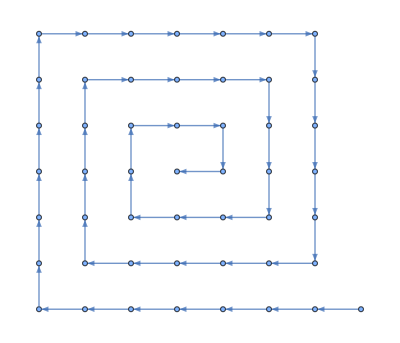

```mathematica
(* 21.6 *) Graph[Table[i->i+1,{i,1,49}]]
```

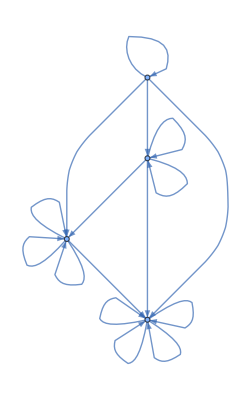

```mathematica
(* 21.7 *) Graph[Flatten[Table[i->Max[i,j],{i,4},{j,4}]]]
```

```mathematica
(* 21.8 *) Graph[Flatten[Table[i->j-i,{i,5},{j,5}]]]
```

-Graphics-

```mathematica
(* 21.9 *) Graph[Table[i->RandomInteger[{1,100}],{i,100}]]
```

-Graphics-

```mathematica
(* 21.10 *) Graph[Flatten[Table[{i->RandomInteger[{1,100}],i->RandomInteger[{1,100}]},{i,100}]]]
```

-Graphics-

```mathematica
(* 21.11 *) Grid[Table[FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],i,j],{i,4},{j,4}]]
```

{1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4}

## Exercises from EIWL3 Section 22

```mathematica
(* 22.1 *) LanguageIdentify["ajatella"]
```

Finnish

```mathematica
(* This will be useful in the next two exercises: *)
tigerImage=Entity["TaxonomicSpecies","PantheraTigris::63rj9"][EntityProperty["TaxonomicSpecies","Image"]];
```

```mathematica
(* 22.2 *) ImageIdentify[tigerImage]
```

tiger

```mathematica
(* 22.3 *) 
ImageIdentify[Table[Blur[tigerImage,blur],{blur,5}]]
```

{tiger,tiger,tiger,tiger,swift fox}

```mathematica
(* 22.4 *) Classify["Sentiment", "I'm so happy to be here"]
```

Positive

```mathematica
(* 22.5 *) Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

```mathematica
(* 22.6 *) Nearest[RandomInteger[1000,20],100,3]
```

{120,80,60}

```mathematica
(* 22.7 *) Nearest[RandomColor[10],Red,5]
```

{RGBColor[0.9473005645556669, 0.2772006442844448, 0.3152139075632088],RGBColor[0.6548342725278258, 0.2397322415848977, 0.6410465336745892],RGBColor[0.6373550652219295, 0.8213459579971332, 0.6873027655223296],RGBColor[0.1281620168895239, 0.4482843076975809, 0.28283393223188247],RGBColor[0.15311727912639816, 0.6455373407319449, 0.4868135295145246]}

```mathematica
(* 22.8 *) Nearest[Range[100]^2,2000]
```

{2025}

```mathematica
(* 22.9 *) Nearest[EntityClass["Country","Europe"][EntityProperty["Country","Flag"]],Entity["Country","Brazil"][EntityProperty["Country","Flag"]],3]
```

{-Graphics-,-Graphics-,-Graphics-}

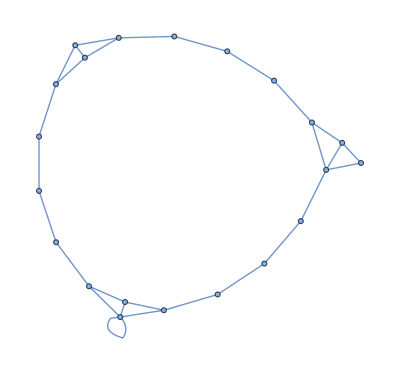

```mathematica
(* 22.10 *) NearestNeighborGraph[Table[Hue[h],{h,0,1,0.05}],2]
```

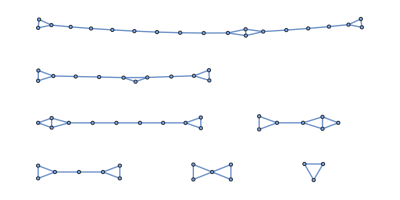

```mathematica
(* 22.11 *) NearestNeighborGraph[RandomInteger[100,100],2]
```


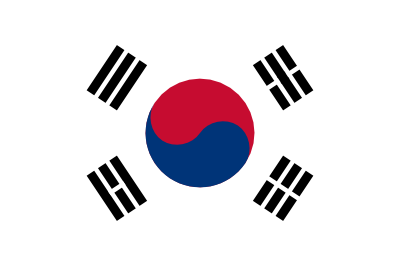
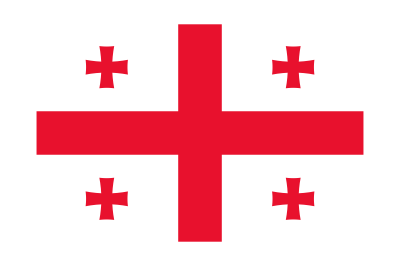
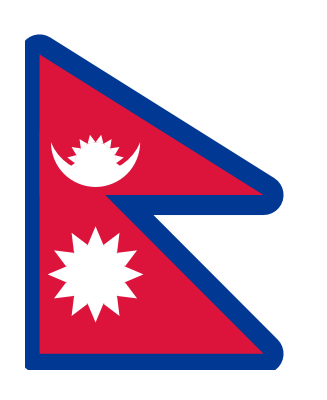
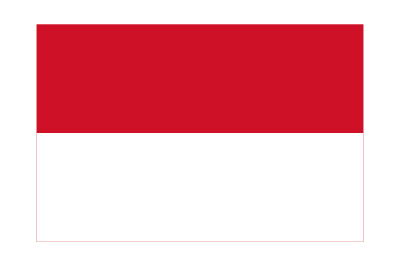
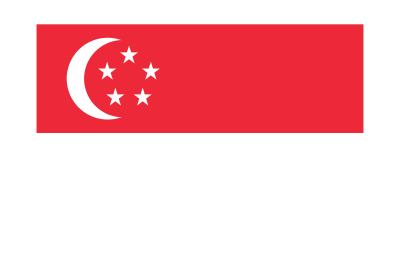
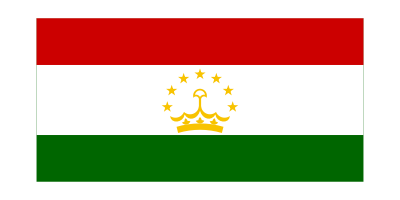
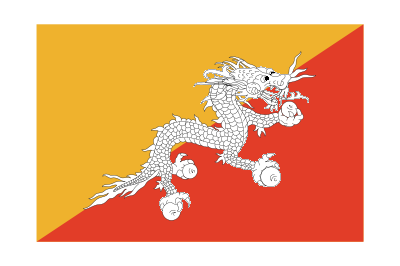
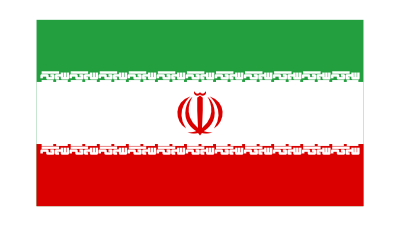

{{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
(* 22.12 *) FindClusters[EntityClass["Country","Asia"][EntityProperty["Country","Flag"]]]
```

```mathematica
Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
(* 22.13 *) Table[Rasterize[letter,RasterSize->20],{letter,Alphabet[]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

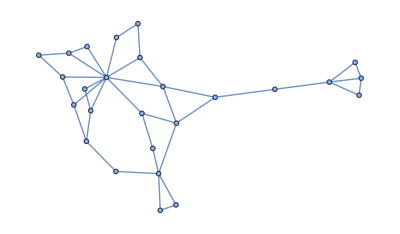

```mathematica
NearestNeighborGraph[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2]
```